# Ex.3 a)

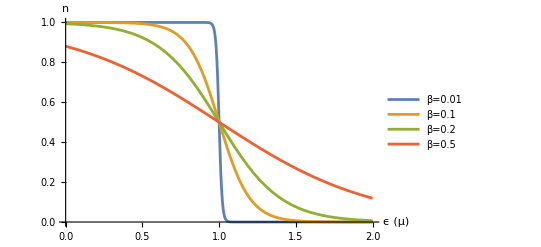

```mathematica
n[e_,T_]:=1/(Exp[(e-1)/T]+1)
Plot[{n[e,0.01],n[e,0.1],n[e,0.2],n[e,0.5]},{e,0,2},PlotLegends->{"β=0.01","β=0.1","β=0.2","β=0.5"},AxesLabel->{"ϵ (μ)","n"}]
```

```mathematica
m:=
M:=
rho:=
hbar:=
NA:=
k:=
T:=
EF=UnitConvert[hbar^2/(2m)*(3Pi^2rho NA/M)^(2/3),"eV"]
TF=UnitConvert[EF/k]
```

0.0000608113 eV

0.705686 K

```mathematica
P=UnitConvert[2/5*EF*rho/M*NA+Pi^2rho*NA*k^2*T^2/(6*M*EF),"bar"]
```

2.45927×10^6 bar

# Ex.4

```mathematica
ClearAll["Global`*"]
Upot:=-3/5G*M^2/R
EF:=(9Pi n/4)^(2/3)hbar^2/(2m R^2)
Ukin:=3/5n*EF
sol=Solve[D[Ukin+Upot,R]==0,R][[1]][[1]]
```

R→(3 (3/2)^(1/3) hbar^2 n^(5/3) π^(2/3))/(2 G m M^2)

```mathematica
m:=
hbar:=
k:=
G:=
c:=
M:=
n:=M/m
R/.sol//UnitConvert
UnitConvert[EF/.sol,"MeV"]
UnitConvert[EF/k/.sol]
β=UnitConvert[Sqrt[EF*2/m]/c/.sol]
```

12300. m

56. MeV

6.5×10^11 K

0.346

Bei β = 0.346 (maximalgeschwindigkeit im fermigas) müsste man relativistische Effekte berücksichtigen